```mathematica
data3 =ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\steel\\Steel.txt",{Number,Number}];
data4=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\steel\\Parab.txt",{Number,Number}];
data5=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\steel\\LogSteel.txt",{Number,Number}];
data6=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\steel\\LogParab.txt",{Number,Number}];
data7=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\steel\\delSteel.txt",{Number,Number}];
data8=ReadList["C:\\Users\\Коптутер\\Desktop\\Универ\\Теорвер\\steel\\delParab.txt",{Number,Number}];
```

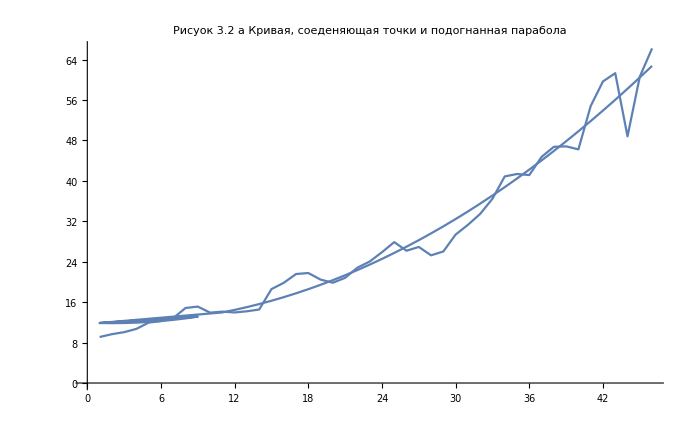

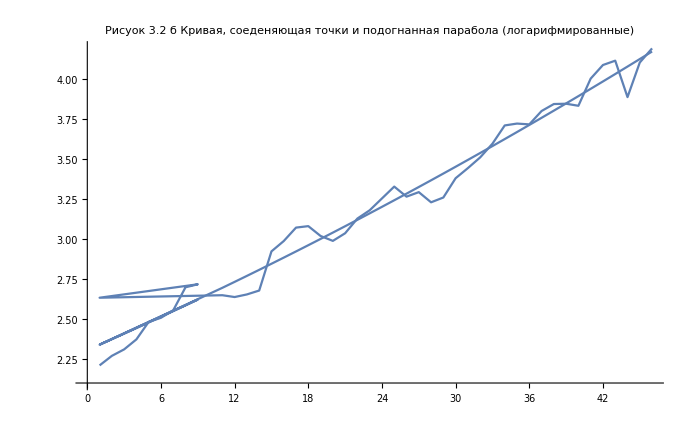

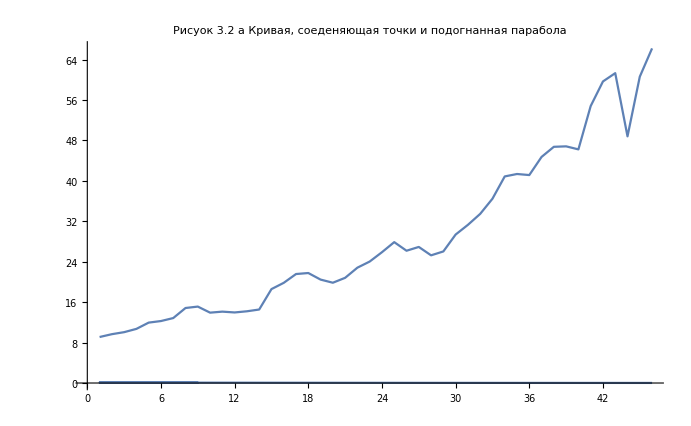

```mathematica
w = ListLinePlot[data3, PlotLabel-> "Рисуок 3.2 а Кривая, соеденяющая точки и подогнанная парабола"];
r = ListLinePlot[data4];
q = ListLinePlot[data5,PlotLabel-> "Рисуок 3.2 б Кривая, соеденяющая точки и подогнанная парабола (логарифмированные)"];
t =ListLinePlot[data6];
f = ListLinePlot[data7];
u =ListLinePlot[data8];
Show[w, r]
Show[q,t]
Show[w, u]
```